Shapefiles downloaded from: https://www.census.gov/cgi-bin/geo/shapefiles/

```mathematica
mapDir=FileNameJoin[{NotebookDirectory[],"shapefiles"}];
```

```mathematica
figDir=FileNameJoin[{NotebookDirectory[],"figs"}];
```

```mathematica
districts=Import[FileNameJoin[{mapDir,"tl_2025_17_cd119.zip"}],{"SHP","Data"}][[1,2,2]];
districts=Most[districts];(*The last one appears to just be water in Lake Michigan*)
```

```mathematica
districtColors=FindVertexColoring[AdjacencyGraph@Boole@Outer[Not@*DisjointQ,districts[[All,1,1]],districts[[All,1,1]],1],ColorData[116,"ColorList"]];
```

```mathematica
tracts=Import[FileNameJoin[{mapDir,"tl_2025_17_tract.zip"}],{"SHP","Data"}][[1,2,2]];
```

```mathematica
blocks=Import[FileNameJoin[{mapDir,"tl_2025_17_tabblock20.zip"}],{"SHP","Data"}][[1,2,2]];
```

```mathematica
GeoGraphics[{
GeoStyling[Opacity[1]],
Transpose[{districtColors,districts}]
}
]//EchoTiming
```

2.17683

-Graphics-

```mathematica
nf=Nearest@Catenate[MapIndexed[Thread[Cases[#1,{_Real,_Real},Infinity]->First[#2]]&,blocks]]
```

NearestFunction[{2, <>}]

```mathematica
(*center=GeoPosition[{41.795108,-87.594540}];*)
center=GeoPosition[{41.795108,-87.6}];
map=GeoGraphics[{
GeoStyling[Opacity[1]],
Transpose[{districtColors,districts}],
{FaceForm[],EdgeForm[Directive[Thickness[0.002],Black]],blocks[[Union@nf[center[[1]],50000]]]},
{FaceForm[],EdgeForm[Directive[Thickness[0.0035],StandardRed]],tracts}
},
GeoRange->Quantity[1.3,"Miles"],
GeoCenter->center,
AspectRatio->1/GoldenRatio,
(*GeoBackground->"VectorMinimalNoLabels"*)
GeoBackground->LightBlue,
Background->None,
ImageSize->600
]//EchoTiming
```

4.26831

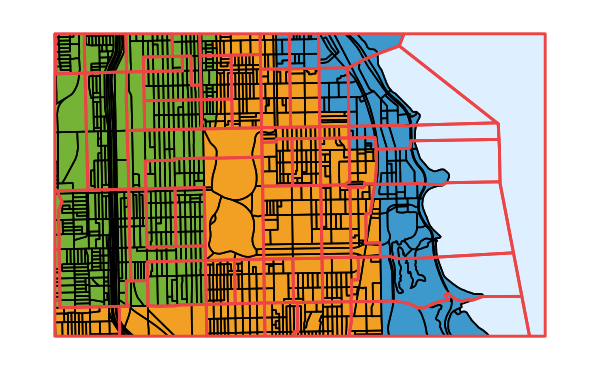

```mathematica
Export[FileNameJoin[{figDir,"blockTractDistrictMap.pdf"}],map];
Export[FileNameJoin[{figDir,"blockTractDistrictMap.png"}],map,RasterSize->1000];
```

```mathematica
(*center=GeoPosition[{41.795108,-87.594540}];*)
center=GeoPosition[{41.795108,-87.6}];
map=GeoGraphics[{
GeoStyling[Opacity[1]],
Transpose[{districtColors,districts}],
{FaceForm[],EdgeForm[Directive[Thickness[0.002],Black]],blocks[[Union@nf[center[[1]],50000]]]}
},
GeoRange->Quantity[1.3,"Miles"],
GeoCenter->center,
AspectRatio->1/GoldenRatio,
(*GeoBackground->"VectorMinimalNoLabels"*)
GeoBackground->LightBlue,
ImageSize->600
]//EchoTiming
```

0.909569

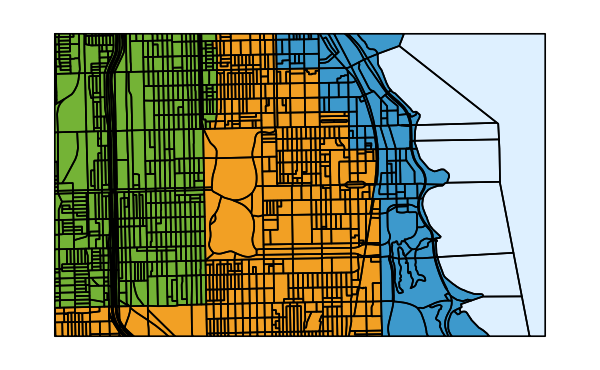

```mathematica
Export[FileNameJoin[{figDir,"blockDistrictMap.pdf"}],map];
Export[FileNameJoin[{figDir,"blockDistrictMap.png"}],map,RasterSize->1000];
```

```mathematica
(*center=GeoPosition[{41.795108,-87.594540}];*)
center=GeoPosition[{41.795108,-87.6}];
map=GeoGraphics[{
GeoStyling[Opacity[1]],
{RGBColor[1.,0.93,0.82],districts},
{FaceForm[],EdgeForm[Directive[Thickness[0.002],Black]],blocks[[Union@nf[center[[1]],50000]]]}
},
GeoRange->Quantity[1.3,"Miles"],
GeoCenter->center,
AspectRatio->1/GoldenRatio,
(*GeoBackground->"VectorMinimalNoLabels",*)
GeoBackground->LightBlue,
GeoBackground->Transparent,Background->Transparent,
ImageSize->600
]//EchoTiming
```

0.917944

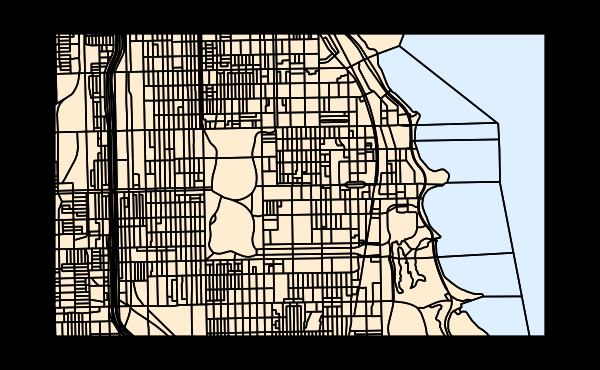

```mathematica
Export[FileNameJoin[{figDir,"blockMap.pdf"}],map];
Export[FileNameJoin[{figDir,"blockMap.png"}],map,RasterSize->1000];
```

```mathematica
(*center=GeoPosition[{41.795108,-87.594540}];*)
center=GeoPosition[{41.795108,-87.6}];
map=GeoGraphics[{
GeoStyling[Opacity[1]],
Transpose[{districtColors,districts}],
{FaceForm[],EdgeForm[Directive[Thickness[0.0035],StandardRed]],tracts}
},
GeoRange->Quantity[1.3,"Miles"],
GeoCenter->center,
AspectRatio->1/GoldenRatio,
(*GeoBackground->"VectorMinimalNoLabels"*)
GeoBackground->LightBlue,
Background->None,
ImageSize->600
]//EchoTiming
```

3.53747

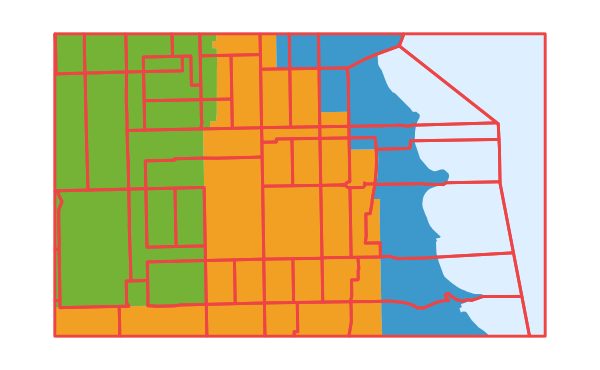

```mathematica
Export[FileNameJoin[{figDir,"tractDistrictMap.pdf"}],map];
Export[FileNameJoin[{figDir,"tractDistrictMap.png"}],map,RasterSize->1000];
```

```mathematica
(*center=GeoPosition[{41.795108,-87.594540}];*)
center=GeoPosition[{41.795108,-87.6}];
map=GeoGraphics[{
GeoStyling[Opacity[1]],
Transpose[{districtColors,districts}]
},
GeoRange->Quantity[1.3,"Miles"],
GeoCenter->center,
AspectRatio->1/GoldenRatio,
(*GeoBackground->"VectorMinimalNoLabels"*)
GeoBackground->LightBlue,
Background->None,
ImageSize->600
]//EchoTiming
```

0.424838

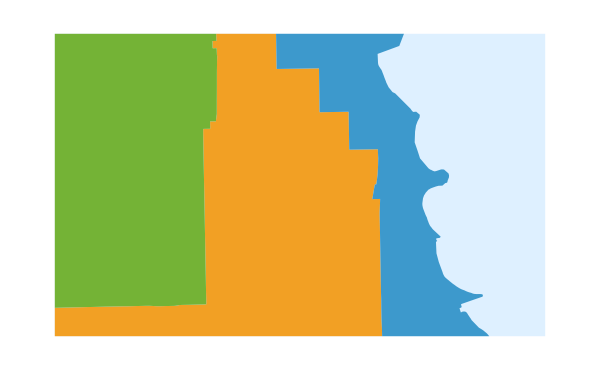

```mathematica
Export[FileNameJoin[{figDir,"districtMap.pdf"}],map];
Export[FileNameJoin[{figDir,"districtMap.png"}],map,RasterSize->1000];
```

```mathematica
(*center=GeoPosition[{41.795108,-87.594540}];*)
center=GeoPosition[{41.795108,-87.6}];
map=GeoGraphics[{
GeoStyling[Opacity[1]],
{RGBColor[1.,0.93,0.82],districts}
},
GeoRange->Quantity[1.3,"Miles"],
GeoCenter->center,
AspectRatio->1/GoldenRatio,
(*GeoBackground->"VectorMinimalNoLabels",*)
GeoBackground->LightBlue,
GeoBackground->Transparent,Background->Transparent,
ImageSize->600
]//EchoTiming
```

0.419063

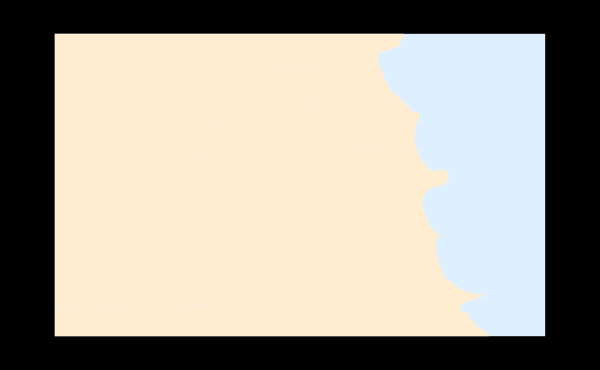

```mathematica
Export[FileNameJoin[{figDir,"baseMap.pdf"}],map];
Export[FileNameJoin[{figDir,"baseMap.png"}],map,RasterSize->1000];
```